```mathematica
F0[x_,T_]:=((π^2 T^2)/12+T (-x^2/(4 T)-x Log[1+ⅇ^(-x/T)]+x Log[Cosh[x/(2 T)]]+T PolyLog[2,-ⅇ^(-x/T)]));
int0[ee_,T_,p_,a_,b_]:=Cos[p]/(2T)Exp[(-F0[(a+b)/Sqrt[2],T]+F0[(a-b)/Sqrt[2],T])/(ee Cos[p])]/Cosh[(a-b)/Sqrt[2]/2/T]^2;
curacc0[ee_,T_]:=Quiet[NIntegrate[2int0[ee,T,p,a,b],{p,0,Pi/2},{a,-Max[10Sqrt[ee],Min[3000*ee/T,20]],Max[10Sqrt[ee],Min[3000*ee/T,20]]},{b,0,Max[10Sqrt[ee],Min[1000*ee/T,20]]},AccuracyGoal->5,PrecisionGoal->5]];
curtest0[ee_,T_,l_]:=Quiet[NIntegrate[2int0[ee,T,p,a,b],{p,0,Pi/2},{a,-l,l},{b,0,l},AccuracyGoal->5,PrecisionGoal->5]]
curtest1[ee_,T_,l_,acc_]:=Quiet[NIntegrate[2int0[ee,T,p,a,b],{p,0,Pi/2},{a,-l,l},{b,0,l},AccuracyGoal->acc,PrecisionGoal->acc]]
```

```mathematica
tabetlow=ParallelTable[{0.01i,curacc0[0.01i,1]},{i,1,100}];
tabetmid=ParallelTable[{1+0.5i,curacc0[1+0.5i,1]},{i,1,200}];
tabethigh=ParallelTable[{100+20i,curacc0[100+20i,1]},{i,1,8}];
tabet=Join[tabetlow,tabetmid,tabethigh];
```

```mathematica
tabetlow05=ParallelTable[{0.01i,curacc0[0.01i,0.5]},{i,1,100}];
tabetmid05=ParallelTable[{1+0.5i,curacc0[1+0.5i,0.5]},{i,1,100}];
tabet05=Join[tabetlow05,tabetmid05];
```

```mathematica
tabetlow3=ParallelTable[{0.01i,curacc0[0.01i,3]},{i,1,100}];
tabetmid3=ParallelTable[{1+0.5i,curacc0[1+0.5i,3]},{i,1,200}];
tabethigh3=ParallelTable[{100+20i,curacc0[100+20i,3]},{i,1,50}];
tabet3=Join[tabetlow3,tabetmid3,tabethigh3];
```

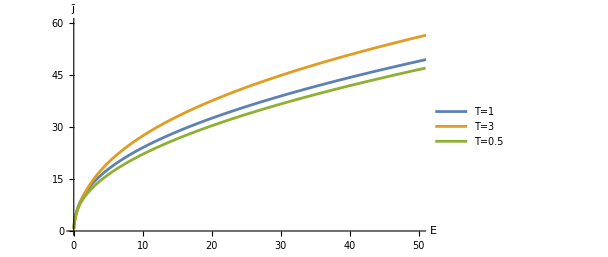

```mathematica
ListLinePlot[{tabet,tabet3,tabet05[[1;;200]]},PlotRange->{{0,50},{0,60}},LabelStyle->{FontFamily->"Arial",FontSize->20,Black},AxesLabel->{"Ē","j̄"},AxesStyle->{{Black,Thick},{Black,Thick}},ImageSize->450,AspectRatio->1/1.75,PlotLegends->Placed[{"T̄=1","T̄=3","T̄=0.5"},{0.85,0.25}]]
```

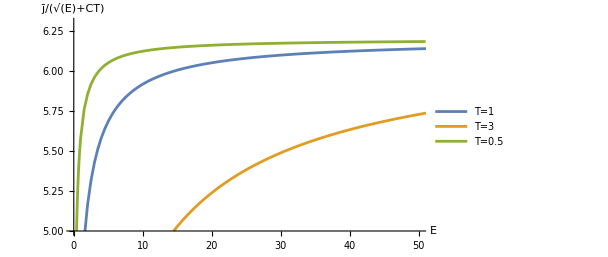

```mathematica
ListLinePlot[{Table[{tabet[[i,1]],tabet[[i,2]]/(Sqrt[tabet[[i,1]]]+0.894869)},{i,1,Length[tabet]}],Table[{tabet3[[i,1]],tabet3[[i,2]]/(Sqrt[tabet3[[i,1]]]+3*0.894869)},{i,1,Length[tabet]}],Table[{tabet05[[i,1]],tabet05[[i,2]]/(Sqrt[tabet05[[i,1]]]+0.5*0.894869)},{i,1,200}]},LabelStyle->{FontFamily->"Arial",FontSize->20,Black},AxesLabel->{"Ē","j̄/(√(Ē)+CT̄)"},AxesStyle->{{Black,Thick},{Black,Thick}},ImageSize->450,AspectRatio->1/1.75,PlotLegends->Placed[{"T̄=1","T̄=3","T̄=0.5"},{0.85,0.25}],PlotRange->{{0,50},{5,6.3}}]
```

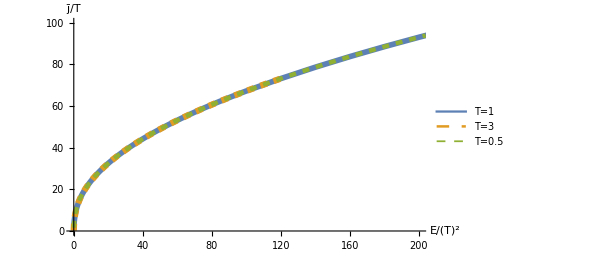

```mathematica
ListLinePlot[{Table[{tabet[[i,1]],tabet[[i,2]]},{i,1,Length[tabet]}],Table[{tabet3[[i,1]]/3^2,tabet3[[i,2]]/3},{i,1,Length[tabet3]}],Table[{tabet05[[i,1]]/0.5^2,tabet05[[i,2]]/0.5},{i,1,200}]},LabelStyle->{FontFamily->"Arial",FontSize->20,Black},AxesLabel->{"Ē/(T̄)^2","j̄/T̄"},AxesStyle->{{Black,Thick},{Black,Thick}},ImageSize->450,AspectRatio->1/1.75,PlotLegends->Placed[{"T̄=1","T̄=3","T̄=0.5"},{0.8,0.5}],PlotRange->{{0,200},{0,100}},PlotStyle->{Thickness[0.009],{Thickness[0.01],Dashed},{Thickness[0.007],Dashed}}]
```

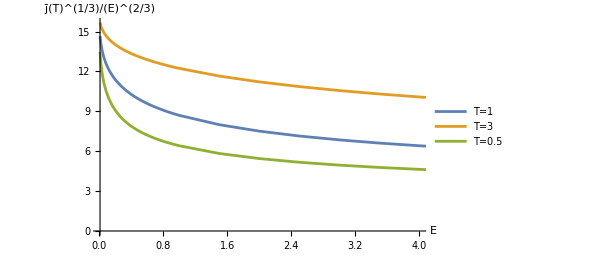

```mathematica
ListLinePlot[{Table[{tabet[[i,1]],tabet[[i,2]]/tabet[[i,1]]^(2/3)},{i,1,Length[tabet]}],Table[{tabet3[[i,1]],tabet3[[i,2]]/tabet3[[i,1]]^(2/3)*3^(1/3)},{i,1,Length[tabet3]}],Table[{tabet05[[i,1]],tabet05[[i,2]]/tabet05[[i,1]]^(2/3)*(0.5)^(1/3)},{i,1,200}]},LabelStyle->{FontFamily->"Arial",FontSize->20,Black},AxesLabel->{"Ē","j̄(T̄)^(1/3)/(Ē)^(2/3)"},AxesStyle->{{Black,Thick},{Black,Thick}},ImageSize->450,AspectRatio->1/1.75,PlotLegends->Placed[{"T̄=1","T̄=3","T̄=0.5"},{0.85,0.7}],PlotRange->{{0.01,4},All}]
```

```mathematica
tabet3={{0.01,0.5045218525589664},{0.02,0.7905338641514628},{0.03,1.0179002769612604},{0.04,1.2282256762537975},{0.05,1.4136802861933018},{0.06,1.585010018605685},{0.07,1.745303893710117},{0.08,1.8966367398653852},{0.09,2.040482293468841},{0.1,2.1779386879462184},{0.11,2.3098514778175416},{0.12,2.436881321836716},{0.13,2.5595789138756757},{0.14,2.6783780963811},{0.15,2.793644530712113},{0.16,2.905701708371536},{0.17,3.0148173016035544},{0.18,3.12121213018913},{0.19,3.225094278369113},{0.2,3.3266327007737115},{0.21,3.4259946386860074},{0.22,3.5233093123239643},{0.23,3.618709178092674},{0.24,3.7123054640532036},{0.25,3.8041906557920298},{0.26,3.8944611800429283},{0.27,3.983203409321264},{0.28,4.070490134937265},{0.29,4.15638971339786},{0.3,4.240970345664359},{0.31,4.324291619486008},{0.32,4.406405083760337},{0.33,4.487362219238749},{0.34,4.5672098157437135},{0.35000000000000003,4.645995407434989},{0.36,4.723755545201162},{0.37,4.800532821384214},{0.38,4.8763597004925705},{0.39,4.951271857975516},{0.4,5.025302706091585},{0.41000000000000003,5.09847848009859},{0.42,5.170829760817985},{0.43,5.242382388035374},{0.44,5.313157736253745},{0.45,5.383192359702618},{0.46,5.452496134784722},{0.47000000000000003,5.521099042735757},{0.48,5.58901179729493},{0.49,5.656260682758242},{0.5,5.722862135411369},{0.51,5.788838643341401},{0.52,5.854198225374243},{0.53,5.918959893329879},{0.54,5.983135092359581},{0.55,6.046762995646574},{0.56,6.109829385419901},{0.5700000000000001,6.172354083080175},{0.58,6.234358474008677},{0.59,6.295844520376069},{0.6,6.356831433587215},{0.61,6.417329496699911},{0.62,6.477344645734173},{0.63,6.536891579318357},{0.64,6.595977408708075},{0.65,6.654624985880971},{0.66,6.712829013942417},{0.67,6.770604041649703},{0.68,6.8279559433145725},{0.6900000000000001,6.884901049293082},{0.7000000000000001,6.94143665985082},{0.71,6.997580149438096},{0.72,7.053333188738393},{0.73,7.108704762809692},{0.74,7.163701212413484},{0.75,7.218331878637166},{0.76,7.272603417029255},{0.77,7.326521905774113},{0.78,7.3800907793736865},{0.79,7.433322953667378},{0.8,7.486217085010785},{0.81,7.538776357673116},{0.8200000000000001,7.591016361214932},{0.8300000000000001,7.6429374177339735},{0.84,7.694553076310788},{0.85,7.745854539870715},{0.86,7.796860236744279},{0.87,7.847557224285622},{0.88,7.89797247140833},{0.89,7.948124587197763},{0.9,7.997929229417949},{0.91,8.047485598419264},{0.92,8.096767704015988},{0.93,8.145784454465252},{0.9400000000000001,8.194529801068816},{0.9500000000000001,8.243011791394027},{0.96,8.291231768101474},{0.97,8.339203320648462},{0.98,8.386918276990981},{0.99,8.434331987094405},{1.,8.481608871731165},{1.5,10.590037234192671},{2.,12.34716313836457},{2.5,13.875173894009375},{3.,15.238789158064046},{3.5,16.477185487958263},{4.,17.616265806832658},{4.5,18.686339836229585},{5.,19.686861670580083},{5.5,20.62844509594137},{6.,21.519309594149348},{6.5,22.365959773004505},{7.,23.173663319642458},{7.5,23.946796918652808},{8.,24.688941595722586},{8.5,25.403035595194194},{9.,26.09170347525191},{9.5,26.757667642739268},{10.,27.402100351415527},{10.5,28.027043512644987},{11.,28.63395280606862},{11.5,29.22415740732816},{12.,29.79873806451041},{12.5,30.358760121883346},{13.,30.905204698177485},{13.5,31.438874205303136},{14.,31.960490314921888},{14.5,32.47101088609578},{15.,32.97069476063722},{15.5,33.46030916926417},{16.,33.940304207614375},{16.5,34.41124315680833},{17.,34.87353087594727},{17.5,35.32759012253977},{18.,35.773798604865625},{18.5,36.21251465638829},{19.,36.64406548583811},{19.5,37.0680353072818},{20.,37.4868762748388},{20.5,37.898723963093936},{21.,38.30443693433416},{21.5,38.70438788845301},{22.,39.09874962671883},{22.5,39.48775720097655},{23.,39.87154028373058},{23.5,40.24932629804955},{24.,40.62426001426872},{24.5,40.99353969495098},{25.,41.358313960201286},{25.5,41.71872163847098},{26.,42.0749012157831},{26.5,42.427006421844226},{27.,42.775149574519716},{27.5,43.11944845525941},{28.,43.460073733582554},{28.5,43.796984507485824},{29.,44.13042806114549},{29.5,44.460457971401354},{30.,44.787169233910895},{30.5,45.11065329909596},{31.,45.43097363282439},{31.5,45.74830215635178},{32.,46.06261962143798},{32.5,46.37402893531405},{33.,46.6826133115052},{33.5,46.988446866214524},{34.,47.291592663863504},{34.5,47.59211579198592},{35.,47.8898336131252},{35.5,48.18550945112389},{36.,48.4785391922118},{36.5,48.76920287759601},{37.,49.057451693571345},{37.5,49.343471015239075},{38.,49.62725553567356},{38.5,49.90882269129943},{39.,50.188299401786985},{39.5,50.46572044203749},{40.,50.741046652806446},{40.5,51.014366750237},{41.,51.28572395983682},{41.5,51.55517823613121},{42.,51.82277918764571},{42.5,52.08846660772741},{43.,52.35235343487622},{43.5,52.61446514767569},{44.,52.87482604609832},{44.5,53.13343926562168},{45.,53.39044062309656},{45.5,53.64576549687598},{46.,53.899471514336646},{46.5,54.15157961100775},{47.,54.402123367955},{47.5,54.651126276907924},{48.,54.89874994907818},{48.5,55.14462601188551},{49.,55.38918174022375},{49.5,55.632471671567565},{50.,55.87401626951408},{50.5,56.11434536609605},{51.,56.35330724966179},{51.5,56.59091982374919},{52.,56.82721251757887},{52.5,57.062209462214696},{53.,57.295923780860875},{53.5,57.528379368897525},{54.,57.759590568470145},{54.5,57.989580206462044},{55.,58.21836867518195},{55.5,58.44595456008865},{56.,58.672386111836616},{56.5,58.897665141324126},{57.,59.12183835444629},{57.5,59.34486547955662},{58.,59.56679068770938},{58.5,59.78762925824016},{59.,60.007396997526065},{59.5,60.22610677923495},{60.,60.44376323427899},{60.5,60.660402620523264},{61.,60.87603302552061},{61.5,61.09065876271281},{62.,61.30429290385625},{62.5,61.51694920738126},{63.,61.7286491065124},{63.5,61.93924257165613},{64.,62.14930219210675},{64.5,62.35811250361537},{65.,62.56609351722876},{65.5,62.773174000666586},{66.,62.979359898137524},{66.5,63.18467215335157},{67.,63.389114837603664},{67.5,63.59260735009354},{68.,63.795417347105776},{68.5,63.997313848172745},{69.,64.19838257220123},{69.5,64.39858784578546},{70.,64.59803812465181},{70.5,64.796679488216},{71.,64.9945270357142},{71.5,65.19159769062998},{72.,65.38790045136703},{72.5,65.58346148557592},{73.,65.77824737604858},{73.5,65.97228411418841},{74.,66.16558689250499},{74.5,66.35815917596192},{75.,66.55005894368888},{75.5,66.74120254865888},{76.,66.93163798303137},{76.5,67.12137084809376},{77.,67.31041320810078},{77.5,67.49877487883681},{78.,67.68643594742086},{78.5,67.87344897459121},{79.,68.05980304757671},{79.5,68.24548523480843},{80.,68.43052708572453},{80.5,68.61492978444569},{81.,68.79869780670731},{81.5,68.98183509439235},{82.,69.16434903721974},{82.5,69.34624797450873},{83.,69.5275368038733},{83.5,69.70821760082441},{84.,69.8882989122311},{84.5,70.067785722741},{85.,70.2466523749179},{85.5,70.42497002575439},{86.,70.6027634797399},{86.5,70.77993056479639},{87.,70.9565279520197},{87.5,71.1325716356754},{88.,71.30805892228454},{88.5,71.48299700241127},{89.,71.65738966297369},{89.5,71.83124202212294},{90.,72.00455571772996},{90.5,72.17734250877112},{91.,72.34960309575351},{91.5,72.5213437356592},{92.,72.69256460535009},{92.5,72.86327501952826},{93.,73.033481668379},{93.5,73.20317875067202},{94.,73.37238056994379},{94.5,73.54108476355378},{95.,73.70927769157338},{95.5,73.87698630714108},{96.,74.04423412647962},{96.5,74.21102710258343},{97.,74.37731951168433},{97.5,74.54314697529574},{98.,74.70849919222006},{98.5,74.87339539945089},{99.,75.03783332623426},{99.5,75.20181687128462},{100.,75.36535027529023},{100.5,75.52843454295225},{101.,75.6910941646288},{120,81.57375823966254},{140,87.2426541280772},{160,92.49137758592893},{180,97.40066853935903},{200,102.02866061024307},{220,106.41852402941863},{240,110.60349952823003},{260,114.60977237831838},{280,118.45845962536987},{300,122.16664546537336},{320,125.74882253811495},{340,129.21686030009397},{360,132.58109402746317},{380,135.85027569434376},{400,139.03200903494368},{420,142.13299943949767},{440,145.15908118209134},{460,148.11543142488895},{480,151.00663382856047},{500,153.83684502650493},{520,156.6097582449051},{540,159.3287219557134},{560,161.99671583555119},{580,164.616656838572},{600,167.19088501040954},{620,169.72177549341163},{640,172.21143354634896},{660,174.66182865539392},{680,177.07483438180478},{700,179.4519156972514},{720,181.79476348781952},{740,184.10481900887947},{760,186.3834295506018},{780,188.63174334450312},{800,190.85110617326927},{820,193.0422695823563},{840,195.2068551699959},{860,197.34535297854487},{880,199.4589603226396},{900,201.54824424694257},{920,203.61416788062652},{940,205.65749630086597},{960,207.67885189226777},{980,209.67911453833335},{1000,211.65884526742087},{1020,213.61867659448177},{1040,215.55918086514498},{1060,217.4809036504128},{1080,219.3843918561312},{1100,221.27017928721952}};
```

```mathematica
tabet05={{0.01,0.7878329093553788},{0.02,1.176625817904552},{0.03,1.476776594851645},{0.04,1.7286448169541744},{0.05,1.9488123438790381},{0.06,2.146094295875376},{0.07,2.3258538164671907},{0.08,2.4916620570548202},{0.09,2.6460172441659506},{0.1,2.790774950146255},{0.11,2.9273375761772433},{0.12,3.056798713564437},{0.13,3.180045297037849},{0.14,3.29778706621289},{0.15,3.410623736852803},{0.16,3.5190410635211937},{0.17,3.62353744187811},{0.18,3.724215901230697},{0.19,3.8216619932582123},{0.2,3.9160498632375256},{0.21,4.007578785646768},{0.22,4.096566252729048},{0.23,4.183091078945446},{0.24,4.2673427431606195},{0.25,4.349484509482248},{0.26,4.429644685978906},{0.27,4.507933004607875},{0.28,4.584474374546025},{0.29,4.6593521390409505},{0.3,4.732668803580961},{0.31,4.804504233775676},{0.32,4.87493262297218},{0.33,4.944023532466399},{0.34,5.011843428946859},{0.35000000000000003,5.078451659002154},{0.36,5.1439037610701766},{0.37,5.208250577985036},{0.38,5.271539882543778},{0.39,5.333816207112575},{0.4,5.395121649531486},{0.41000000000000003,5.455496984541793},{0.42,5.514980833183921},{0.43,5.573604579905952},{0.44,5.63139541007933},{0.45,5.688390530611027},{0.46,5.744618670302916},{0.47000000000000003,5.800103381656671},{0.48,5.854873369929653},{0.49,5.908957261079848},{0.5,5.962360387006046},{0.51,6.01512344932853},{0.52,6.067261888510515},{0.53,6.1187912963324615},{0.54,6.169733949471909},{0.55,6.220106154963397},{0.56,6.269925687206829},{0.5700000000000001,6.319209962680258},{0.58,6.367967873701779},{0.59,6.416224421080865},{0.6,6.463972195492413},{0.61,6.511266528063228},{0.62,6.558081478270249},{0.63,6.604442735715884},{0.64,6.650360990117862},{0.65,6.695844004210772},{0.66,6.740910169115367},{0.67,6.785567090928904},{0.68,6.829825545590069},{0.6900000000000001,6.873691875711933},{0.7000000000000001,6.917180762405898},{0.71,6.960292810932494},{0.72,7.003047800071064},{0.73,7.045440351280399},{0.74,7.0874884795720146},{0.75,7.129199993426676},{0.76,7.1705795166999735},{0.77,7.210431745440884},{0.78,7.252383513089225},{0.79,7.292794915118081},{0.8,7.3329142435799275},{0.81,7.372737248142061},{0.8200000000000001,7.4122666690008145},{0.8300000000000001,7.451508935840473},{0.84,7.490472902731119},{0.85,7.529162498138516},{0.86,7.567582573725721},{0.87,7.605741247984438},{0.88,7.64363619212643},{0.89,7.681275446134428},{0.9,7.718649679495176},{0.91,7.7558097736567175},{0.92,7.7927135037350705},{0.93,7.829380785156898},{0.9400000000000001,7.865816008133093},{0.9500000000000001,7.9020210626589025},{0.96,7.938012027334975},{0.97,7.9737732486560695},{0.98,8.00931702929752},{0.99,8.044644022807894},{1.,8.07976518334379},{1.5,9.626597567865153},{2.,10.897990076906238},{2.5,12.000755941784218},{3.,12.987224910042352},{3.5,13.88745392641004},{4.,14.72050268902458},{4.5,15.499409123371963},{5.,16.23344475655978},{5.5,16.929533527074582},{6.,17.592980862711208},{6.5,18.227974215640845},{7.,18.837883231517893},{7.5,19.425450481260423},{8.,19.992959812174725},{8.5,20.54233672565344},{9.,21.075196706454133},{9.5,21.592966185265816},{10.,22.096849004577116},{10.5,22.587901596896724},{11.,23.067015912806664},{11.5,23.535142149097386},{12.,23.992881843925222},{12.5,24.440946244221774},{13.,24.87991594784328},{13.5,25.3103218970533},{14.,25.732648267474225},{14.5,26.14733709553445},{15.,26.554786992618844},{15.5,26.955359215086865},{16.,27.349401521695018},{16.5,27.7372077955411},{17.,28.11908024916584},{17.5,28.495271185803666},{18.,28.866041876830955},{18.5,29.23159526029474},{19.,29.592182730475795},{19.5,29.94795337974952},{20.,30.29912724796984},{20.5,30.645874947846313},{21.,30.988362312572484},{21.5,31.3267296536298},{22.,31.661132447328566},{22.5,31.991702483767355},{23.,32.3185382911101},{23.5,32.64184818690982},{24.,32.96167163386685},{24.5,33.278159992766376},{25.,33.591374041157216},{25.5,33.90155313134399},{26.,34.20843521481709},{26.5,34.51244991462517},{27.,34.81358408891293},{27.5,35.111916904795855},{28.,35.40751738400554},{28.5,35.700471216219626},{29.,35.99083499591072},{29.5,36.27867748915695},{30.,36.564065309355},{30.5,36.84706373909552},{31.,37.12772953375151},{31.5,37.406117489890946},{32.,37.68228443165396},{32.5,37.95634365042752},{33.,38.228170444912664},{33.5,38.4979726902713},{34.,38.76575677574659},{34.5,39.03158690348626},{35.,39.29543014658023},{35.5,39.557404387000446},{36.,39.81753619960923},{36.5,40.07583815024747},{37.,40.33236040871807},{37.5,40.58714917768344},{38.,40.84022421829851},{38.5,41.09163189907673},{39.,41.341399196223584},{39.5,41.58954196464721},{40.,41.83613659571263},{40.5,42.081184604578674},{41.,42.324687183720386},{41.5,42.566720572487874},{42.,42.80728357644981},{42.5,43.04640658083063},{43.,43.28411465957429},{43.5,43.520442138986134},{44.,43.75540076579984},{44.5,43.98902060750251},{45.,44.22131985939009},{45.5,44.45232684804206},{46.,44.682059640270595},{46.5,44.910537664648956},{47.,45.1377839727931},{47.5,45.36381776244227},{48.,45.58865765708483},{48.5,45.81232314458794},{49.,46.034836848233994},{49.5,46.25619775676635},{50.,46.476445682702106},{50.5,46.695588048418735},{51.,46.91364071195769}};
```

```mathematica
tabet={{0.01,0.6804205572992202},{0.02,1.0409395768105603},{0.03,1.328537698130145},{0.04,1.5756435945446619},{0.05,1.7957397853648336},{0.06,1.9959872139342343},{0.07,2.1808393390395677},{0.08,2.353254624736496},{0.09,2.515337728363743},{0.1,2.6686614673278344},{0.11,2.8144172632487394},{0.12,2.953553245536857},{0.13,3.0868348852973573},{0.14,3.214884110435425},{0.15,3.338222504935205},{0.16,3.4572901246417502},{0.17,3.572470347384737},{0.18,3.6840647519423486},{0.19,3.7923682758409076},{0.2,3.8976296234163597},{0.21,4.000054415294004},{0.22,4.09984732371922},{0.23,4.1971736400880415},{0.24,4.292187987947701},{0.25,4.385029158789124},{0.26,4.4758219578462555},{0.27,4.564680132021565},{0.28,4.651709809721383},{0.29,4.737005460503177},{0.3,4.820657397252651},{0.31,4.9027346804797105},{0.32,4.983322644741064},{0.33,5.062494152303632},{0.34,5.140287446305683},{0.35000000000000003,5.216785495856939},{0.36,5.292038272152231},{0.37,5.366092154552631},{0.38,5.439001248096582},{0.39,5.510805794823254},{0.4,5.5815469110755025},{0.41000000000000003,5.65127362263707},{0.42,5.7200096691017475},{0.43,5.787797937987161},{0.44,5.854671015204473},{0.45,5.920658782686398},{0.46,5.985792294598987},{0.47000000000000003,6.0500965526961865},{0.48,6.1135990647834975},{0.49,6.176329051336306},{0.5,6.238304574911091},{0.51,6.299548402109407},{0.52,6.3600881349894545},{0.53,6.419941095225712},{0.54,6.479126704940167},{0.55,6.537664967388575},{0.56,6.59557094173021},{0.5700000000000001,6.652865107664646},{0.58,6.709563507265531},{0.59,6.76567826327676},{0.6,6.821228477516163},{0.61,6.876227828616676},{0.62,6.930691063999148},{0.63,6.984629535912238},{0.64,7.038067343034652},{0.65,7.090993420058508},{0.66,7.143420832040984},{0.67,7.195381847249376},{0.68,7.246880292586495},{0.6900000000000001,7.297924230661},{0.7000000000000001,7.3485260254903695},{0.71,7.398690460165934},{0.72,7.448430788358276},{0.73,7.497755166106631},{0.74,7.546673129483598},{0.75,7.595195126379694},{0.76,7.643316547609856},{0.77,7.691072605400622},{0.78,7.738449456386622},{0.79,7.785449703211645},{0.8,7.83209833673335},{0.81,7.878404992415327},{0.8200000000000001,7.924340414929191},{0.8300000000000001,7.969944302677351},{0.84,8.015166925083914},{0.85,8.060176700652937},{0.86,8.104806618330642},{0.87,8.149121602444835},{0.88,8.1931289914376},{0.89,8.236831510882482},{0.9,8.280235314547967},{0.91,8.323347056183882},{0.92,8.366176423355556},{0.93,8.408702346037222},{0.9400000000000001,8.450977720615723},{0.9500000000000001,8.492968790946069},{0.96,8.534686116337854},{0.97,8.576145140946544},{0.98,8.61733691226258},{0.99,8.658276124692},{1.,8.698967522918565},{1.5,10.480046363280268},{2.,11.924722815628062},{2.5,13.16262870001388},{3.,14.258400826655445},{3.5,15.24943601421526},{4.,16.159513064070566},{4.5,17.00478891674569},{5.,17.79681354103226},{5.5,18.544157223855827},{6.,19.253196856156706},{6.5,19.929209752746704},{7.,20.5762163688375},{7.5,21.19753578336454},{8.,21.795966817122256},{8.5,22.373790282697954},{9.,22.93289926890246},{9.5,23.474990008584893},{10.,24.00151857257678},{10.5,24.51369492118456},{11.,25.012611108744775},{11.5,25.499235652051123},{12.,25.974453476087735},{12.5,26.438972027849378},{13.,26.893491327117466},{13.5,27.338621255065387},{14.,27.77483252846567},{14.5,28.202802117840754},{15.,28.622874778600824},{15.5,29.035483575431645},{16.,29.441005378049137},{16.5,29.839794032491888},{17.,30.232164272594588},{17.5,30.61841872992994},{18.,30.998818246743916},{18.5,31.37364789811975},{19.,31.743123077101437},{19.5,32.10746528458147},{20.,32.46688951311958},{20.5,32.82158771917396},{21.,33.171692502606106},{21.5,33.51752450227947},{22.,33.85906705414917},{22.5,34.196555075381475},{23.,34.53010594969382},{23.5,34.859867112593484},{24.,35.1859617254224},{24.5,35.508507940361646},{25.,35.82761724608706},{25.5,36.143393213171905},{26.,36.455948431281705},{26.5,36.76537668767721},{27.,37.0717611377644},{27.5,37.37520247530752},{28.,37.67576646303579},{28.5,37.973539625936645},{29.,38.268606860425386},{29.5,38.561039846298335},{30.,38.85090096252081},{30.5,39.13824947907225},{31.,39.42316359832556},{31.5,39.70550731221706},{32.,39.985919624349435},{32.5,40.26386708847403},{33.,40.5395900429089},{33.5,40.81317228764495},{34.,41.08467345130688},{34.5,41.35409638906611},{35.,41.62147414739164},{35.5,41.88690191535903},{36.,42.150393412908265},{36.5,42.41201722001945},{37.,42.671782993655654},{37.5,42.92974254582562},{38.,43.18593237053162},{38.5,43.440394754477296},{39.,43.6931494687814},{39.5,43.94424036969873},{40.,44.19369800915432},{40.5,44.44155268949541},{41.,44.68783556582804},{41.5,44.93257621332812},{42.,45.17580319379345},{42.5,45.41754174897553},{43.,45.65782123645082},{43.5,45.89666976332025},{44.,46.134031825613285},{44.5,46.37016407078964},{45.,46.60486287846251},{45.5,46.83822495100823},{46.,47.07028429819476},{46.5,47.301030717148976},{47.,47.53051791281426},{47.5,47.75875447252506},{48.,47.985763687850486},{48.5,48.21156219830159},{49.,48.436174347924556},{49.5,48.659610190808856},{50.,48.88189248844354},{50.5,49.10301321368941},{51.,49.32306578333512},{51.5,49.54199191125589},{52.,49.75983189568656},{52.5,49.976603675463686},{53.,50.19232009969694},{53.5,50.40698922787965},{54.,50.62064379410663},{54.5,50.833287679555234},{55.,51.044860148132166},{55.5,51.25560083709652},{56.,51.4652965349485},{56.5,51.67403918237121},{57.,51.88184905748956},{57.5,52.08871988768586},{58.,52.29467419106884},{58.5,52.49972519970405},{59.,52.703887368027786},{59.5,52.907166063257904},{60.,53.1095739852377},{60.5,53.31113115657888},{61.,53.511832025010854},{61.5,53.71168253428411},{62.,53.91071843017371},{62.5,54.10894249303233},{63.,54.30635750414038},{63.5,54.5029772787713},{64.,54.69880304339001},{64.5,54.89385312253119},{65.,55.08813352134813},{65.5,55.28164599501684},{66.,55.47441559108214},{66.5,55.66644267841179},{67.,55.85774260950993},{67.5,56.04831030535122},{68.,56.23816049833165},{68.5,56.42730177075532},{69.,56.615738207305014},{69.5,56.803483486965796},{70.,56.99054237160732},{70.5,57.17692183752509},{71.,57.36263272718405},{71.5,57.5476951654372},{72.,57.73208375366195},{72.5,57.91563261812081},{73.,58.09870803054823},{73.5,58.28136050562844},{74.,58.46319052058948},{74.5,58.644395840760545},{75.,58.824986800092375},{75.5,59.004984635332946},{76.,59.18436546095153},{76.5,59.36311923484825},{77.,59.54129762556108},{77.5,59.71889267234343},{78.,59.895906759499056},{78.5,60.07211151510142},{79.,60.248216017412716},{79.5,60.42350964087685},{80.,60.59825449593968},{80.5,60.77244731122016},{81.,60.946047692037574},{81.5,61.119146053277596},{82.,61.29174989569263},{82.5,61.46377933255164},{83.,61.63528217896626},{83.5,61.80626741423202},{84.,61.976724625144946},{84.5,62.146667393700604},{85.,62.31609583968533},{85.5,62.48502811637879},{86.,62.653459307259574},{86.5,62.821378822392276},{87.,62.98883094725331},{87.5,63.1557918675958},{88.,63.322264894657216},{88.5,63.48825695307993},{89.,63.65377645972995},{89.5,63.818822976604864},{90.,63.98340496753475},{90.5,64.14749317388724},{91.,64.31115732122856},{91.5,64.4743215303042},{92.,64.6370765822202},{92.5,64.79942483885016},{93.,64.96128761936325},{93.5,65.12271058428692},{94.,65.28369637381964},{94.5,65.44421689999659},{95.,65.60436962154365},{95.5,65.7640663641742},{96.,65.92334326773366},{96.5,66.08223770124592},{97.,66.24068064669356},{97.5,66.3987064777747},{98.,66.5563199855328},{98.5,66.71351860184288},{99.,66.87032523841631},{99.5,67.0267399253743},{100.,67.18274808231435},{100.5,67.33836189410665},{101.,67.4935880267871},{120,73.12813061871},{140,78.59086029316038},{160,83.67227319142529},{180,88.44263971878017},{200,92.95289136540434},{220,97.24146366426987},{240,101.33815906809767},{260,105.26661666980525}}
```